```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];
spvstecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
spvstecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
spvstecratio3 = Flatten[Import["chianti10.1_APO_sp_emissline3_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
opvstecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];



spvsnecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
spvsnecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
spvsnecratio3 = Flatten[Import["chianti10.1_APO_sp_emissline3_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
opvsnecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];



spvstecratiolist =Table[{Tec[[i]],spvstecratio[[i]]},{i,1,Length[Tec],1}];
spvstecratiolist2 =Table[{Tec[[i]],spvstecratio2[[i]]},{i,1,Length[Tec],1}];
spvstecratiolist3 =Table[{Tec[[i]],spvstecratio3[[i]]},{i,1,Length[Tec],1}];
opvstecratiolist =Table[{Tec[[i]],opvstecratio[[i]]},{i,1,Length[Tec],1}];
spvsnecratiolist =Table[{nec[[i]],spvsnecratio[[i]]},{i,1,Length[nec],1}];
spvsnecratiolist2 =Table[{nec[[i]],spvsnecratio2[[i]]},{i,1,Length[nec],1}];
spvsnecratiolist3=Table[{nec[[i]],spvsnecratio3[[i]]},{i,1,Length[nec],1}];
opvsnecratiolist =Table[{nec[[i]],opvsnecratio[[i]]},{i,1,Length[nec],1}];
spvstecratioint=Interpolation[spvstecratiolist];
spvstecratioint2=Interpolation[spvstecratiolist2];
spvstecratioint3=Interpolation[spvstecratiolist3];
opvstecratioint=Interpolation[opvstecratiolist];
spvsnecratioint=Interpolation[spvsnecratiolist];
spvsnecratioint2=Interpolation[spvsnecratiolist2];
spvsnecratioint3=Interpolation[spvsnecratiolist3];
opvsnecratioint=Interpolation[opvsnecratiolist];


ymin=0.4(*0.001;*)
ymax=30;

manualTicksY={{0.4,"0.4",0.02},{0.5,"",0.01},{0.6,"",0.01},{0.7,"",0.01},{0.8,"",0.01},{0.9,"",0.01},{1,"1",0.02},{2,"",0.01},{3,"",0.01},{4,"",0.01},{5,"",0.01},{6,"",0.01},{7,"",0.01},{8,"",0.01},{9,"",0.01},{10,"10",0.02},{20,"",0.01},{30,"30",0.02}};

manualTicksY2={{0.4,"",0.02},{0.5,"",0.01},{0.6,"",0.01},{0.7,"",0.01},{0.8,"",0.01},{0.9,"",0.01},{1,"",0.02},{2,"",0.01},{3,"",0.01},{4,"",0.01},{5,"",0.01},{6,"",0.01},{7,"",0.01},{8,"",0.01},{9,"",0.01},{10,"",0.02},{20,"",0.01},{30,"",0.02}};

fsfs=12;
insetfontsize=12;

(*{{left,right},{bottom,top}}*)
impad = {{36,19},{38,6}};(*{{45,17},{37,4}};*)
ypl=11;(*2.35*)


xpleg =0.5;(*0.8;*)
ypleg =0.37;(*0.43;*)

thickval=0.0075;
lfsize = 8;
lmsize = 5;

colors={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]}; 

p55=Plot[{spvstecratioint[x],1/spvstecratioint2[x],1/spvstecratioint3[x],opvstecratioint[x]},{x,0.1,1000},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{Automatic,{ymin,ymax}},FrameTicks->{{manualTicksY,manualTicksY},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"T_ec (eV)","Emissivity Ratios"},Epilog->Inset[Style["n_ec=2000 cm^-3",Bold,FontSize->insetfontsize],{Log10[30],Log10[ypl]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6716/6731Å","S^+ 6731/4076Å","S^+ 6731/4069Å","O^+ 3729/3726Å"},Range[4]}],LegendMarkerSize->lmsize,LegendLayout->{"Row",2}],Scaled[{xpleg,ypleg}]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[2]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]]}];
p66=Plot[{spvsnecratioint[x],1/spvsnecratioint2[x],1/spvsnecratioint3[x],opvsnecratioint[x]},{x,1,10000},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{Automatic,{ymin,ymax}},FrameTicks->{{manualTicksY,manualTicksY},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"n_ec (cm^-3)",""},Epilog->Inset[Style["T_ec=5 eV",Bold,FontSize->insetfontsize],{Log10[100],Log10[ypl]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[2]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]]}];

ResourceFunction["PlotGrid"][{{p55,p66}}]
```

/Users/edne8319/Desktop/emissiontables_CITEP_2_

0.4

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];
effemisscoefsvstec = Transpose[ Import["APO_eff_emiss_coeffs_vs_tec_57x8.csv","CSV"]];

effemisscoefsvsnec = Transpose[ Import["APO_eff_emiss_coeffs_vs_nec_61x8.csv","CSV"]];
colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 

eec1vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,1]]},{i,1,Length[Tec],1}];
eec2vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,2]]},{i,1,Length[Tec],1}];
eec3vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,3]]},{i,1,Length[Tec],1}];
eec4vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,4]]},{i,1,Length[Tec],1}];
eec5vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,5]]},{i,1,Length[Tec],1}];
eec6vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,6]]},{i,1,Length[Tec],1}];
eec7vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,7]]},{i,1,Length[Tec],1}];
eec8vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,8]]},{i,1,Length[Tec],1}];

eec1vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,1]]},{i,1,Length[nec],1}];
eec2vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,2]]},{i,1,Length[nec],1}];
eec3vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,3]]},{i,1,Length[nec],1}];
eec4vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,4]]},{i,1,Length[nec],1}];
eec5vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,5]]},{i,1,Length[nec],1}];
eec6vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,6]]},{i,1,Length[nec],1}];
eec7vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,7]]},{i,1,Length[nec],1}];
eec8vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,8]]},{i,1,Length[nec],1}];

eec1vstec=Interpolation[eec1vsteclist];
eec2vstec=Interpolation[eec2vsteclist];
eec3vstec=Interpolation[eec3vsteclist];
eec4vstec=Interpolation[eec4vsteclist];
eec5vstec=Interpolation[eec5vsteclist];
eec6vstec=Interpolation[eec6vsteclist];
eec7vstec=Interpolation[eec7vsteclist];
eec8vstec=Interpolation[eec8vsteclist];

eec1vsnec=Interpolation[eec1vsneclist];
eec2vsnec=Interpolation[eec2vsneclist];
eec3vsnec=Interpolation[eec3vsneclist];
eec4vsnec=Interpolation[eec4vsneclist];
eec5vsnec=Interpolation[eec5vsneclist];
eec6vsnec=Interpolation[eec6vsneclist];
eec7vsnec=Interpolation[eec7vsneclist];
eec8vsnec=Interpolation[eec8vsneclist];




fsfs=8;
insetfontsize=7.5;

(*{{left,right},{bottom,top}}*)
impad = {{52,35},{31,5}};(*{{45,17},{37,4}};*)
ypl=3*10^-8;(*2.35*)
ypl1=2.7*10^-8;(*2.35*)
ymin=5*10^-11;
ymax=5*10^-8;

xpleg =0.45;
ypleg =0.39;

thickval=0.0075;
lmsize = 2;
lfsize=6.;

p55=Plot[{eec8vstec[x],eec7vstec[x],eec6vstec[x],eec5vstec[x],eec4vstec[x],eec3vstec[x],eec2vstec[x],eec1vstec[x]},{x,0.1,600},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{{0.1,1000},{ymin,ymax}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"T_ec (eV)","Photons cm^3 s^-1"},Epilog->Inset[Style["n_ec=2000 cm^-3",Bold,FontSize->insetfontsize],{Log10[10],Log10[ypl1]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]}];
p66=Plot[{eec8vsnec[x],eec7vsnec[x],eec6vsnec[x],eec5vsnec[x],eec4vsnec[x],eec3vsnec[x],eec2vsnec[x],eec1vsnec[x]},{x,1,10000},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{Automatic,{ymin,ymax}},FrameTicks->{{Automatic,All},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"n_ec (cm^-3)",""},Epilog->Inset[Style["T_ec=5 eV",Bold,FontSize->insetfontsize],{Log10[2000],Log10[ypl]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize,LegendLayout->{"Row",4}],Scaled[{xpleg,ypleg}]]];


ResourceFunction["PlotGrid"][{{p55,p66}},FrameLabel->{{"",""},{"","Effective Emission Coefficients"}},FrameStyle->Directive[Black,Bold,FontSize->fsfs]]
```

/Users/edne8319/Desktop/emissiontables_CITEP_2_

-Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/edne8319/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];


effemisscoefsvstec = Transpose[ Import["APO_eff_emiss_coeffs_vs_tec_57x8.csv","CSV"]];

effemisscoefsvsnec = Transpose[ Import["APO_eff_emiss_coeffs_vs_nec_61x8.csv","CSV"]];


eec1vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,1]]},{i,1,Length[Tec],1}];
eec2vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,2]]},{i,1,Length[Tec],1}];
eec3vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,3]]},{i,1,Length[Tec],1}];
eec4vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,4]]},{i,1,Length[Tec],1}];
eec5vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,5]]},{i,1,Length[Tec],1}];
eec6vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,6]]},{i,1,Length[Tec],1}];
eec7vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,7]]},{i,1,Length[Tec],1}];
eec8vsteclist=Table[{Tec[[i]],effemisscoefsvstec[[i,8]]},{i,1,Length[Tec],1}];

eec1vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,1]]},{i,1,Length[nec],1}];
eec2vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,2]]},{i,1,Length[nec],1}];
eec3vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,3]]},{i,1,Length[nec],1}];
eec4vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,4]]},{i,1,Length[nec],1}];
eec5vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,5]]},{i,1,Length[nec],1}];
eec6vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,6]]},{i,1,Length[nec],1}];
eec7vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,7]]},{i,1,Length[nec],1}];
eec8vsneclist=Table[{nec[[i]],effemisscoefsvsnec[[i,8]]},{i,1,Length[nec],1}];

eec1vstec=Interpolation[eec1vsteclist,InterpolationOrder->1];
eec2vstec=Interpolation[eec2vsteclist,InterpolationOrder->1];
eec3vstec=Interpolation[eec3vsteclist,InterpolationOrder->1];
eec4vstec=Interpolation[eec4vsteclist,InterpolationOrder->1];
eec5vstec=Interpolation[eec5vsteclist,InterpolationOrder->1];
eec6vstec=Interpolation[eec6vsteclist,InterpolationOrder->1];
eec7vstec=Interpolation[eec7vsteclist,InterpolationOrder->1];
eec8vstec=Interpolation[eec8vsteclist,InterpolationOrder->1];

eec1vsnec=Interpolation[eec1vsneclist,InterpolationOrder->1];
eec2vsnec=Interpolation[eec2vsneclist,InterpolationOrder->1];
eec3vsnec=Interpolation[eec3vsneclist,InterpolationOrder->1];
eec4vsnec=Interpolation[eec4vsneclist,InterpolationOrder->1];
eec5vsnec=Interpolation[eec5vsneclist,InterpolationOrder->1];
eec6vsnec=Interpolation[eec6vsneclist,InterpolationOrder->1];
eec7vsnec=Interpolation[eec7vsneclist,InterpolationOrder->1];
eec8vsnec=Interpolation[eec8vsneclist,InterpolationOrder->1];




effemisscoefsvstechote1 = Transpose[ Import["APO_eff_emiss_coeffs_vs_tec_57x8_feh=0.0025_Teh=45eV.csv","CSV"]];

effemisscoefsvsnechote1 = Transpose[ Import["APO_eff_emiss_coeffs_vs_nel_61x8_feh=0.0025_Teh=45eV.csv","CSV"]];


eec1vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,1]]},{i,1,Length[Tec],1}];
eec2vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,2]]},{i,1,Length[Tec],1}];
eec3vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,3]]},{i,1,Length[Tec],1}];
eec4vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,4]]},{i,1,Length[Tec],1}];
eec5vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,5]]},{i,1,Length[Tec],1}];
eec6vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,6]]},{i,1,Length[Tec],1}];
eec7vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,7]]},{i,1,Length[Tec],1}];
eec8vsteclisthote1=Table[{Tec[[i]],effemisscoefsvstechote1[[i,8]]},{i,1,Length[Tec],1}];

eec1vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,1]]},{i,1,Length[nec],1}];
eec2vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,2]]},{i,1,Length[nec],1}];
eec3vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,3]]},{i,1,Length[nec],1}];
eec4vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,4]]},{i,1,Length[nec],1}];
eec5vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,5]]},{i,1,Length[nec],1}];
eec6vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,6]]},{i,1,Length[nec],1}];
eec7vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,7]]},{i,1,Length[nec],1}];
eec8vsneclisthote1=Table[{nec[[i]],effemisscoefsvsnechote1[[i,8]]},{i,1,Length[nec],1}];

eec1vstechote1=Interpolation[eec1vsteclisthote1,InterpolationOrder->1];
eec2vstechote1=Interpolation[eec2vsteclisthote1,InterpolationOrder->1];
eec3vstechote1=Interpolation[eec3vsteclisthote1,InterpolationOrder->1];
eec4vstechote1=Interpolation[eec4vsteclisthote1,InterpolationOrder->1];
eec5vstechote1=Interpolation[eec5vsteclisthote1,InterpolationOrder->1];
eec6vstechote1=Interpolation[eec6vsteclisthote1,InterpolationOrder->1];
eec7vstechote1=Interpolation[eec7vsteclisthote1,InterpolationOrder->1];
eec8vstechote1=Interpolation[eec8vsteclisthote1,InterpolationOrder->1];

eec1vsnechote1=Interpolation[eec1vsneclisthote1,InterpolationOrder->1];
eec2vsnechote1=Interpolation[eec2vsneclisthote1,InterpolationOrder->1];
eec3vsnechote1=Interpolation[eec3vsneclisthote1,InterpolationOrder->1];
eec4vsnechote1=Interpolation[eec4vsneclisthote1,InterpolationOrder->1];
eec5vsnechote1=Interpolation[eec5vsneclisthote1,InterpolationOrder->1];
eec6vsnechote1=Interpolation[eec6vsneclisthote1,InterpolationOrder->1];
eec7vsnechote1=Interpolation[eec7vsneclisthote1,InterpolationOrder->1];
eec8vsnechote1=Interpolation[eec8vsneclisthote1,InterpolationOrder->1];


effemisscoefsvstechote2 = Transpose[ Import["APO_eff_emiss_coeffs_vs_tec_57x8_feh=0.01_Teh=300eV.csv","CSV"]];

effemisscoefsvsnechote2 = Transpose[ Import["APO_eff_emiss_coeffs_vs_nel_61x8_feh=0.01_Teh=300eV.csv","CSV"]];


eec1vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,1]]},{i,1,Length[Tec],1}];
eec2vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,2]]},{i,1,Length[Tec],1}];
eec3vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,3]]},{i,1,Length[Tec],1}];
eec4vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,4]]},{i,1,Length[Tec],1}];
eec5vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,5]]},{i,1,Length[Tec],1}];
eec6vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,6]]},{i,1,Length[Tec],1}];
eec7vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,7]]},{i,1,Length[Tec],1}];
eec8vsteclisthote2=Table[{Tec[[i]],effemisscoefsvstechote2[[i,8]]},{i,1,Length[Tec],1}];

eec1vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,1]]},{i,1,Length[nec],1}];
eec2vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,2]]},{i,1,Length[nec],1}];
eec3vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,3]]},{i,1,Length[nec],1}];
eec4vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,4]]},{i,1,Length[nec],1}];
eec5vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,5]]},{i,1,Length[nec],1}];
eec6vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,6]]},{i,1,Length[nec],1}];
eec7vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,7]]},{i,1,Length[nec],1}];
eec8vsneclisthote2=Table[{nec[[i]],effemisscoefsvsnechote2[[i,8]]},{i,1,Length[nec],1}];

eec1vstechote2=Interpolation[eec1vsteclisthote2,InterpolationOrder->1];
eec2vstechote2=Interpolation[eec2vsteclisthote2,InterpolationOrder->1];
eec3vstechote2=Interpolation[eec3vsteclisthote2,InterpolationOrder->1];
eec4vstechote2=Interpolation[eec4vsteclisthote2,InterpolationOrder->1];
eec5vstechote2=Interpolation[eec5vsteclisthote2,InterpolationOrder->1];
eec6vstechote2=Interpolation[eec6vsteclisthote2,InterpolationOrder->1];
eec7vstechote2=Interpolation[eec7vsteclisthote2,InterpolationOrder->1];
eec8vstechote2=Interpolation[eec8vsteclisthote2,InterpolationOrder->1];

eec1vsnechote2=Interpolation[eec1vsneclisthote2,InterpolationOrder->1];
eec2vsnechote2=Interpolation[eec2vsneclisthote2,InterpolationOrder->1];
eec3vsnechote2=Interpolation[eec3vsneclisthote2,InterpolationOrder->1];
eec4vsnechote2=Interpolation[eec4vsneclisthote2,InterpolationOrder->1];
eec5vsnechote2=Interpolation[eec5vsneclisthote2,InterpolationOrder->1];
eec6vsnechote2=Interpolation[eec6vsneclisthote2,InterpolationOrder->1];
eec7vsnechote2=Interpolation[eec7vsneclisthote2,InterpolationOrder->1];
eec8vsnechote2=Interpolation[eec8vsneclisthote2,InterpolationOrder->1];



colors={ColorData[97,"ColorList"][[6]],ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[13]],ColorData[97,"ColorList"][[10]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[9]],ColorData[97,"ColorList"][[14]]}; 
fsfs=12;
insetfontsize=7;

(*{{left,right},{bottom,top}}*)
impad = {{20,20},{40,5}};(*{{45,17},{37,4}};*)
ypl=1.1;(*2.35*)
ypl1=ypl;(*2.35*)
ymin=0.8;
ymax=1.2;

xpleg =0.5;
ypleg =0.4;

thickval=0.0075;
lfsize =7;
lmsize=2.5;

p55=Plot[{eec8vstec[x]/eec8vstechote1[x],eec7vstec[x]/eec7vstechote1[x],eec6vstec[x]/eec6vstechote1[x],eec5vstec[x]/eec5vstechote1[x],eec4vstec[x]/eec4vstechote1[x],eec3vstec[x]/eec3vstechote1[x],eec2vstec[x]/eec2vstechote1[x],eec1vstec[x]/eec1vstechote1[x]},{x,0.1,600},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{{0.1,1000},{ymin,ymax}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},Epilog->Inset[Style["n_eTotal=2000 cm^-3, F_eh=0.25%, T_eh=45 eV",Bold,FontSize->insetfontsize],{Log10[10],Log10[ypl1]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]}];
p66=Plot[{eec8vsnec[x]/eec8vsnechote1[x],eec7vsnec[x]/eec7vsnechote1[x],eec6vsnec[x]/eec6vsnechote1[x],eec5vsnec[x]/eec5vsnechote1[x],eec4vsnec[x]/eec4vsnechote1[x],eec3vsnec[x]/eec3vsnechote1[x],eec2vsnec[x]/eec2vsnechote1[x],eec1vsnec[x]/eec1vsnechote1[x]},{x,1,10000},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{Automatic,{ymin,ymax}},FrameTicks->{{Automatic,All},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"",""},Epilog->Inset[Style["T_ec=5 eV, F_eh=0.25%, T_eh=45 eV",Bold,FontSize->insetfontsize],{Log10[100],Log10[ypl]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]}];



p56=Plot[{eec8vstec[x]/eec8vstechote2[x],eec7vstec[x]/eec7vstechote2[x],eec6vstec[x]/eec6vstechote2[x],eec5vstec[x]/eec5vstechote2[x],eec4vstec[x]/eec4vstechote2[x],eec3vstec[x]/eec3vstechote2[x],eec2vstec[x]/eec2vstechote2[x],eec1vstec[x]/eec1vstechote2[x]},{x,0.1,600},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{{0.1,1000},{ymin,ymax}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"T_ec (eV)",""},Epilog->Inset[Style["n_eTotal=2000 cm^-3, F_eh=1%, T_eh=300 eV",Bold,FontSize->insetfontsize],{Log10[10],Log10[ypl1]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]}];
p67=Plot[{eec8vsnec[x]/eec8vsnechote2[x],eec7vsnec[x]/eec7vsnechote2[x],eec6vsnec[x]/eec6vsnechote2[x],eec5vsnec[x]/eec5vsnechote2[x],eec4vsnec[x]/eec4vsnechote2[x],eec3vsnec[x]/eec3vsnechote2[x],eec2vsnec[x]/eec2vsnechote2[x],eec1vsnec[x]/eec1vsnechote2[x]},{x,1,10000},Frame->True,ScalingFunctions->{"Log10","Log10"},PlotRange->{Automatic,{ymin,ymax}},FrameTicks->{{Automatic,All},{Automatic,Automatic}},ImagePadding->impad,ImageSize->500,AspectRatio->1/GoldenRatio,FrameLabel->{"n_eTotal (cm^-3)",""},Epilog->Inset[Style["T_ec=5 eV, F_eh=1%, T_eh=300 eV",Bold,FontSize->insetfontsize],{Log10[100],Log10[ypl]}],FrameStyle->Directive[Black,Bold,FontSize->fsfs],LabelStyle->Directive[Black,Bold,FontSize->fsfs],FrameTicksStyle->Directive[Black,Bold,FontSize->fsfs],PlotStyle->{Directive[ColorData[97,"ColorList"][[6]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[4]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[13]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[10]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[3]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[1]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[9]],Thickness[thickval]],Directive[ColorData[97,"ColorList"][[14]],Thickness[thickval]]},PlotLegends->Placed[LineLegend[Style[#,FontSize->lfsize,Bold,FontColor->colors[[#2]]]&@@@Transpose[{{"S^+ 6731 Å","S^+ 6716 Å","S^(++) 6312 Å","S^+ 4076 Å","S^+ 4069 Å","O^+ 3729 Å","O^+ 3726 Å","S^(++) 3722 Å"},Range[8]}],LegendMarkerSize->lmsize,LegendLayout->{"Row",3}],Scaled[{xpleg,ypleg}]]];


ResourceFunction["PlotGrid"][{{p55,p66},{p56,p67}},FrameLabel->{"","Single to Double Maxwellian Emiss. Ratio"}]
```

/Users/edne8319/Desktop/emissiontables_CITEP_2_

-Graphics-

Remove::rmnsm: There are no symbols matching "Global`*".

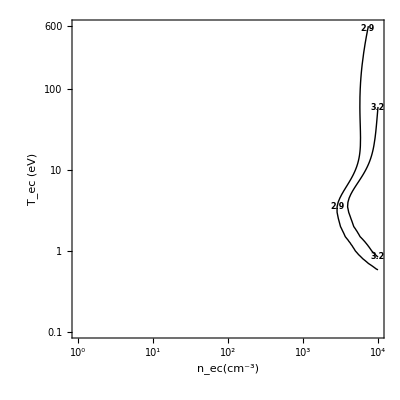

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
ParulaCM=Module[{colorlist},colorlist={{0.2081,0.1663,0.5292},{0.2116238095,0.1897809524,0.5776761905},{0.212252381,0.2137714286,0.6269714286},{0.2081,0.2386,0.6770857143},{0.1959047619,0.2644571429,0.7279},{0.1707285714,0.2919380952,0.779247619},{0.1252714286,0.3242428571,0.8302714286},{0.0591333333,0.3598333333,0.8683333333},{0.0116952381,0.3875095238,0.8819571429},{0.0059571429,0.4086142857,0.8828428571},{0.0165142857,0.4266,0.8786333333},{0.032852381,0.4430428571,0.8719571429},{0.0498142857,0.4585714286,0.8640571429},{0.0629333333,0.4736904762,0.8554380952},{0.0722666667,0.4886666667,0.8467},{0.0779428571,0.5039857143,0.8383714286},{0.079347619,0.5200238095,0.8311809524},{0.0749428571,0.5375428571,0.8262714286},{0.0640571429,0.5569857143,0.8239571429},{0.0487714286,0.5772238095,0.8228285714},{0.0343428571,0.5965809524,0.819852381},{0.0265,0.6137,0.8135},{0.0238904762,0.6286619048,0.8037619048},{0.0230904762,0.6417857143,0.7912666667},{0.0227714286,0.6534857143,0.7767571429},{0.0266619048,0.6641952381,0.7607190476},{0.0383714286,0.6742714286,0.743552381},{0.0589714286,0.6837571429,0.7253857143},{0.0843,0.6928333333,0.7061666667},{0.1132952381,0.7015,0.6858571429},{0.1452714286,0.7097571429,0.6646285714},{0.1801333333,0.7176571429,0.6424333333},{0.2178285714,0.7250428571,0.6192619048},{0.2586428571,0.7317142857,0.5954285714},{0.3021714286,0.7376047619,0.5711857143},{0.3481666667,0.7424333333,0.5472666667},{0.3952571429,0.7459,0.5244428571},{0.4420095238,0.7480809524,0.5033142857},{0.4871238095,0.7490619048,0.4839761905},{0.5300285714,0.7491142857,0.4661142857},{0.5708571429,0.7485190476,0.4493904762},{0.609852381,0.7473142857,0.4336857143},{0.6473,0.7456,0.4188},{0.6834190476,0.7434761905,0.4044333333},{0.7184095238,0.7411333333,0.3904761905},{0.7524857143,0.7384,0.3768142857},{0.7858428571,0.7355666667,0.3632714286},{0.8185047619,0.7327333333,0.3497904762},{0.8506571429,0.7299,0.3360285714},{0.8824333333,0.7274333333,0.3217},{0.9139333333,0.7257857143,0.3062761905},{0.9449571429,0.7261142857,0.2886428571},{0.9738952381,0.7313952381,0.266647619},{0.9937714286,0.7454571429,0.240347619},{0.9990428571,0.7653142857,0.2164142857},{0.9955333333,0.7860571429,0.196652381},{0.988,0.8066,0.1793666667},{0.9788571429,0.8271428571,0.1633142857},{0.9697,0.8481380952,0.147452381},{0.9625857143,0.8705142857,0.1309},{0.9588714286,0.8949,0.1132428571},{0.9598238095,0.9218333333,0.0948380952},{0.9661,0.9514428571,0.0755333333},{0.9763,0.9831,0.0538}};
Evaluate[Blend[RGBColor@@@colorlist,#]&]];

SetDirectory["/Users/edne8319/Desktop/emissiontables_CITEP_2_"];
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];
spratio1 =Transpose[ Import["chianti10.1_APO_sp_6716to6731ang_emiss_ratio_vs_nec_and_Tec_61x57_elements.csv","CSV"]];
spratio2 =Transpose[ Import["chianti10.1_APO_sp_4069to6731ang_emiss_ratio_vs_nec_and_Tec_61x57_elements.csv","CSV"]];
spratio3 =Transpose[ Import["chianti10.1_APO_sp_4076to6731ang_emiss_ratio_vs_nec_and_Tec_61x57_elements.csv","CSV"]];

opratio =Transpose[Import["chianti10.1_APO_op_3729to3726ang_emiss_ratio_vs_nec_and_Tec_61x57_elements.csv","CSV"]];

spratio1list =Flatten[Table[{nec[[i]],Tec[[j]],spratio1[[i,j]]},{i,1,Length[nec],1},{j,1,Length[Tec],1}],1];
spratio2list =Flatten[Table[{nec[[i]],Tec[[j]],1/spratio2[[i,j]]},{i,1,Length[nec],1},{j,1,Length[Tec],1}],1];
spratio3list =Flatten[Table[{nec[[i]],Tec[[j]],1/spratio3[[i,j]]},{i,1,Length[nec],1},{j,1,Length[Tec],1}],1];
opratiolist =Flatten[Table[{nec[[i]],Tec[[j]],opratio[[i,j]]},{i,1,Length[nec],1},{j,1,Length[Tec],1}],1];


spratio4list =Flatten[Table[{nec[[i]],Tec[[j]],spratio1[[i,j]]/spratio2[[i,j]]},{i,1,Length[nec],1},{j,1,Length[Tec],1}],1];
(*Correctly scale values for ParulaCM*)

neclocation1=50;
Teclocation1=100;
neclocation2=20;
Teclocation2=100;
neclocation3=50;
Teclocation3=100;
neclocation4=10;
Teclocation4=100;

contourlabelfontsize=8;
cblabelfsize=12;
axlbfz=14;

zmin1=Min[spratio1list[[All,3]]];
zmax1=Max[spratio1list[[All,3]]];

zmin=0.1;
zmax=100;
insetfontsize=8;
contourlabelfontsize=8;

necmax = 50000;
xpleg1 = 0.904;
xpleg2= xpleg1;
xpleg3 = xpleg1;
xpleg4 = xpleg1;
lmsize1={4.5,150};
lmsize2=lmsize1;
lmsize3=lmsize1;
lmsize4=lmsize1;

cnlfsz =6.75 ;

Tec={0.08,0.1,0.2,0.3,0.4,0.5,0.6,0.7000000000000001,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.};

(*Define manual ticks for the y-axis*)manualTicksY={{0.1,"0.1",0.02},{0.2,"",0.01},{0.3,"",0.01},{0.4,"",0.01},{0.5,"",0.01},{0.6,"",0.01},{0.7,"",0.01},{0.8,"",0.01},{0.9,"",0.01},{1,"1",0.02},{2,"",0.01},{3,"",0.01},{4,"",0.01},{5,"",0.01},{6,"",0.01},{7,"",0.01},{8,"",0.01},{9,"",0.01},{10,"10",0.02},{20,"",0.01},{30,"",0.01},{40,"",0.01},{50,"",0.01},{60,"",0.01},{70,"",0.01},{80,"",0.01},{90,"",0.01},{100,"100",0.02},{200,"",0.01},{300,"",0.01},{400,"",0.01},{500,"",0.01},{600,"600",0.02}};
(*
p1=ListContourPlot[spratio1list,Contours->{0.6,0.8,1.0,1.2,1.4,1.45},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p2=ListDensityPlot[spratio1list,ColorFunction->ParulaCM,ScalingFunctions->{"Log10","Log10","Log10"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize->cnlfsz,FontWeight->"Bold",FontColor->Black},LegendMarkerSize->lmsize1,Method->{TicksStyle->Directive[Black,Bold]}],Scaled[{xpleg1 ,0.5}]],PlotRange->{{Min[nec],necmax},MinMax[Tec],Automatic},Epilog->Inset[Style["S^+ 6716Å/6731Å",Bold,FontSize->insetfontsize],{Log10[neclocation1],Log10[Teclocation1]}],MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p3=Show[p2,p1];


p4=ListContourPlot[spratio2list,Contours->{3,7,10,27},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}]
p5=ListDensityPlot[spratio2list,ColorFunction->ParulaCM,ScalingFunctions->{"Log10","Log10","Log10"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize->cnlfsz,FontWeight->"Bold",FontColor->Black},LegendMarkerSize->lmsize2,Method->{TicksStyle->Directive[Black,Bold]}],Scaled[{xpleg2 ,0.5}]],PlotRange->{{Min[nec],necmax},MinMax[Tec],{2,30}},Epilog->Inset[Style["S^+ 6731Å/4069Å",Bold,FontSize->insetfontsize],{Log10[neclocation2],Log10[Teclocation2]}],MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p6=Show[p5,p4];

p44=ListContourPlot[spratio3list,Contours->{10,20,30,60},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p55=ListDensityPlot[spratio3list,ColorFunction->ParulaCM,ScalingFunctions->{"Log10","Log10","Log10"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize->cnlfsz,FontWeight->"Bold",FontColor->Black},LegendMarkerSize->lmsize3,Method->{TicksStyle->Directive[Black,Bold]}],Scaled[{xpleg3 ,0.5}]],PlotRange->{{Min[nec],necmax},MinMax[Tec],{5,60}},Epilog->Inset[Style["S^+ 6731Å/4076Å",Bold,FontSize->insetfontsize],{Log10[neclocation3],Log10[Teclocation3]}],MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p66=Show[p55,p44];


p7=ListContourPlot[opratiolist,Contours->{0.5,0.7,0.9,1.1,1.3,1.4,1.45},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p8=ListDensityPlot[opratiolist,ColorFunction->ParulaCM,ScalingFunctions->{"Log10","Log10","Log10"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize->cnlfsz,FontWeight->"Bold",FontColor->Black},LabelStyle->{FontSize->cnlfsz,FontWeight->"Bold",FontColor->Black},LegendMarkerSize->lmsize4,Method->{TicksStyle->Directive[Black,Bold]}],Scaled[{xpleg4 ,0.5}]],PlotRange->{{Min[nec],necmax},MinMax[Tec],Automatic},Epilog->Inset[Style["O^+ 3729Å/3726Å",Bold,FontSize->insetfontsize],{Log10[neclocation4],Log10[Teclocation4]}],MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY}];
p9=Show[p8,p7]
(*Grid[{{p3,p6,p9}}]*)

(*Grid[{{p3},{p6},{p9}}]*)

ResourceFunction["PlotGrid"][{{p3,p66},{p6,p9}},FrameLabel->{"n_ec (cm^-3)","T_ec (eV)"},"HideOuterTickLabels"->None,Method->{"AllCustomTicks"->False}] *)(*,FrameTicksStyle->Directive[Black,Bold,FontSize->12],Frame->True,FrameTicks->{Automatic,manualTicksY}]*)
(*ratio1=0.72;
ratio3=24.6;
ratio2=5.36;
ratio4=0.54;
Show[ListContourPlot[spratio1list,Contours->{ratio1},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}],ListContourPlot[spratio2list,Contours->{ratio2},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}],ListContourPlot[spratio3list,Contours->{ratio3},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}],ListContourPlot[opratiolist,Contours->{ratio4},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}]]*)

ratio2=3.2;(*3.2;*)

ratio4=2.9;
Show[ListContourPlot[spratio4list,Contours->{ratio4},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}],ListContourPlot[spratio2list,Contours->{ratio2},ContourShading->None,ContourStyle->Directive[Opacity[1,Black]],ScalingFunctions->{"Log10","Log10","Linear"},FrameStyle->Directive[Black,Bold,FontSize->12],LabelStyle->Directive[Black,Bold,FontSize->12],FrameTicksStyle->Directive[Black,Bold,FontSize->12],ContourLabels->(Text[Style[#3,Bold,contourlabelfontsize],{#1,#2}]&),MaxPlotPoints->Infinity,FrameTicks->{Automatic,manualTicksY},FrameLabel->{"n_ec(cm^-3)","T_ec (eV)"}]]
```

/Users/enerney/Desktop/emissiontables_CITEP_2_

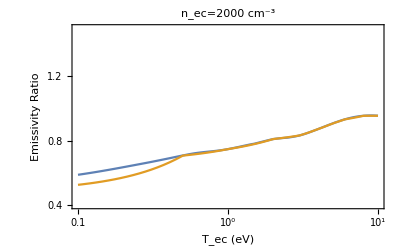
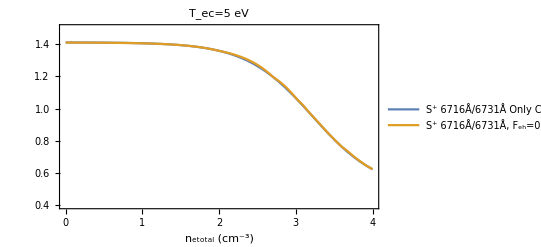
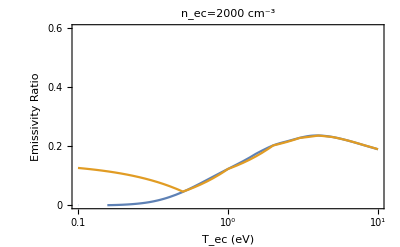
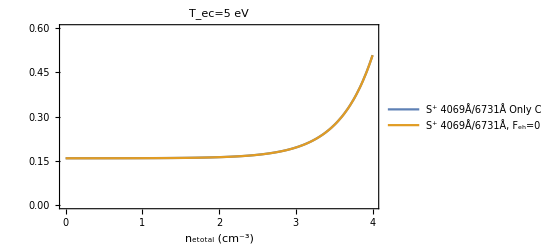
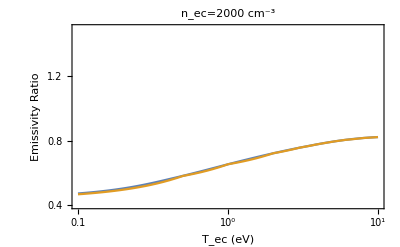
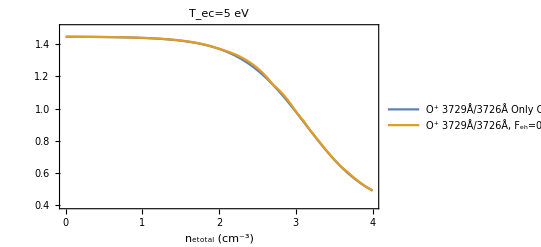
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/enerney/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];

nel2 = Flatten[Import["nel_for_ratio_plots_13_elements.csv","CSV"]];
Tec2 = Flatten[Import["tec_for_ratio_plots_10_elements.csv","CSV"]];

spvstecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
spvstecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
opvstecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];

spvsnecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
spvsnecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
opvsnecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];


spvstecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];
spvstecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];
opvstecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];

spvsnecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];
spvsnecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];
opvsnecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=45eV_lowres.csv","CSV"]];



spvstecratiolist =Table[{Tec[[i]],spvstecratio[[i]]},{i,1,Length[Tec],1}];
spvstecratiolist2 =Table[{Tec[[i]],spvstecratio2[[i]]},{i,1,Length[Tec],1}];
opvstecratiolist =Table[{Tec[[i]],opvstecratio[[i]]},{i,1,Length[Tec],1}];
spvsnecratiolist =Table[{nec[[i]],spvsnecratio[[i]]},{i,1,Length[nec],1}];
spvsnecratiolist2 =Table[{nec[[i]],spvsnecratio2[[i]]},{i,1,Length[nec],1}];
opvsnecratiolist =Table[{nec[[i]],opvsnecratio[[i]]},{i,1,Length[nec],1}];

spvstecratiolisthote =Table[{Tec2[[i]],spvstecratiohote[[i]]},{i,1,Length[Tec2],1}];
spvstecratiolist2hote =Table[{Tec2[[i]],spvstecratio2hote[[i]]},{i,1,Length[Tec2],1}];
opvstecratiolisthote =Table[{Tec2[[i]],opvstecratiohote[[i]]},{i,1,Length[Tec2],1}];

spvsnecratiolisthote =Table[{nel2[[i]],spvsnecratiohote[[i]]},{i,1,Length[nel2],1}];
spvsnecratiolist2hote =Table[{nel2[[i]],spvsnecratio2hote[[i]]},{i,1,Length[nel2],1}];
opvsnecratiolisthote =Table[{nel2[[i]],opvsnecratiohote[[i]]},{i,1,Length[nel2],1}];


spvstecratioint=Interpolation[spvstecratiolist];
spvstecratioint2=Interpolation[spvstecratiolist2];
opvstecratioint=Interpolation[opvstecratiolist];

spvsnecratioint=Interpolation[spvsnecratiolist];
spvsnecratioint2=Interpolation[spvsnecratiolist2];
opvsnecratioint=Interpolation[opvsnecratiolist];

spvstecratiointhote=Interpolation[spvstecratiolisthote,InterpolationOrder->1];
spvstecratioint2hote=Interpolation[spvstecratiolist2hote,InterpolationOrder->1];
opvstecratiointhote=Interpolation[opvstecratiolisthote,InterpolationOrder->1];

spvsnecratiointhote=Interpolation[spvsnecratiolisthote,InterpolationOrder->1];
spvsnecratioint2hote=Interpolation[spvsnecratiolist2hote,InterpolationOrder->1];
opvsnecratiointhote=Interpolation[opvsnecratiolisthote,InterpolationOrder->1];

p1=Plot[{spvstecratioint[x],spvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p2=Plot[{spvsnecratioint[x],spvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"S^+ 6716Å/6731Å Only Core Electrons","S^+ 6716Å/6731Å, F_eh=0.25%, T_eh 45 eV"}];


p3=Plot[{spvstecratioint2[x],spvstecratioint2hote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6}];
p4=Plot[{spvsnecratioint2[x],spvsnecratioint2hote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6},PlotLegends->{"S^+ 4069Å/6731Å Only Core Electrons","S^+ 4069Å/6731Å, F_eh=0.25%, T_eh 45 eV"}];


p5=Plot[{opvstecratioint[x],opvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p6=Plot[{opvsnecratioint[x],opvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"O^+ 3729Å/3726Å Only Core Electrons","O^+ 3729Å/3726Å, F_eh=0.25%, T_eh 45 eV"}];




Grid[{{p1,p2},{p3,p4},{p5,p6}}]
```

```mathematica
spvstecratiolisthote
```

{{0.1,0.526485},{0.5,0.708217},{1.,0.748622},{2.,0.81098},{3.,0.833543},{4.,0.873799},{5.,0.908765},{6.,0.933389},{8.,0.955659},{10.,0.955829}}

```mathematica
spvsnecratiolisthote
```

{{1.,286.993},{100.,277.876},{500.,245.607},{1000.,214.093},{1500.,189.747},{2000.,170.45},{2500.,154.788},{3000.,141.82},{3500.,130.899},{4000.,121.569},{6000.,94.7175},{8000.,77.6364},{10000.,65.7718}}

```mathematica
nel2
```

{1.,100.,500.,1000.,1500.,2000.,2500.,3000.,3500.,4000.,6000.,8000.,10000.}

```mathematica
Tec2
```

{0.1,0.5,1.,2.,3.,4.,5.,6.,8.,10.}

/Users/enerney/Desktop/emissiontables_CITEP_2_

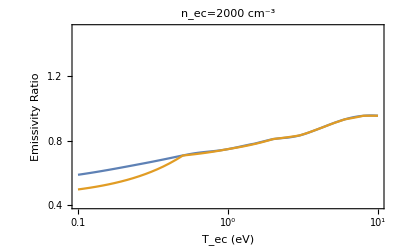
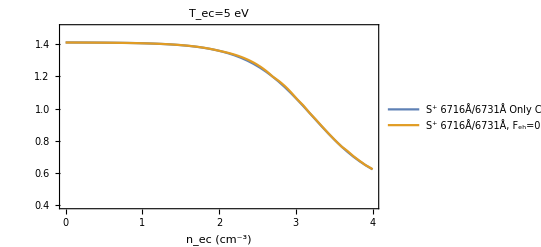
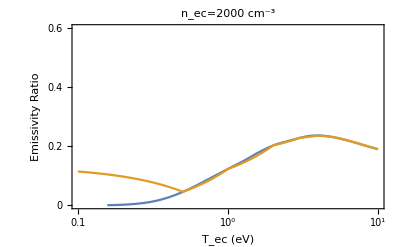
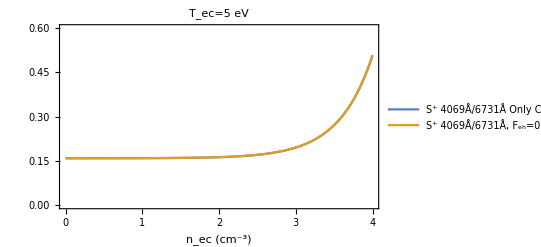
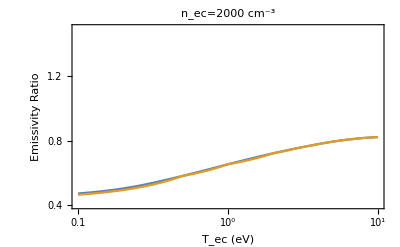
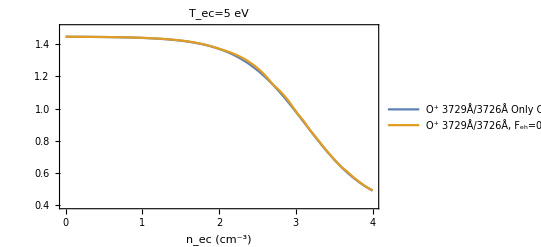
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/enerney/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];

nel2 = Flatten[Import["nel_for_ratio_plots_13_elements.csv","CSV"]];
Tec2 = Flatten[Import["tec_for_ratio_plots_10_elements.csv","CSV"]];

spvstecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
spvstecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
opvstecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];

spvsnecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
spvsnecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
opvsnecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];


spvstecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];
spvstecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];
opvstecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];

spvsnecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];
spvsnecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];
opvsnecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.0025_Teh=300eV_lowres.csv","CSV"]];



spvstecratiolist =Table[{Tec[[i]],spvstecratio[[i]]},{i,1,Length[Tec],1}];
spvstecratiolist2 =Table[{Tec[[i]],spvstecratio2[[i]]},{i,1,Length[Tec],1}];
opvstecratiolist =Table[{Tec[[i]],opvstecratio[[i]]},{i,1,Length[Tec],1}];
spvsnecratiolist =Table[{nec[[i]],spvsnecratio[[i]]},{i,1,Length[nec],1}];
spvsnecratiolist2 =Table[{nec[[i]],spvsnecratio2[[i]]},{i,1,Length[nec],1}];
opvsnecratiolist =Table[{nec[[i]],opvsnecratio[[i]]},{i,1,Length[nec],1}];

spvstecratiolisthote =Table[{Tec2[[i]],spvstecratiohote[[i]]},{i,1,Length[Tec2],1}];
spvstecratiolist2hote =Table[{Tec2[[i]],spvstecratio2hote[[i]]},{i,1,Length[Tec2],1}];
opvstecratiolisthote =Table[{Tec2[[i]],opvstecratiohote[[i]]},{i,1,Length[Tec2],1}];

spvsnecratiolisthote =Table[{nel2[[i]],spvsnecratiohote[[i]]},{i,1,Length[nel2],1}];
spvsnecratiolist2hote =Table[{nel2[[i]],spvsnecratio2hote[[i]]},{i,1,Length[nel2],1}];
opvsnecratiolisthote =Table[{nel2[[i]],opvsnecratiohote[[i]]},{i,1,Length[nel2],1}];


spvstecratioint=Interpolation[spvstecratiolist];
spvstecratioint2=Interpolation[spvstecratiolist2];
opvstecratioint=Interpolation[opvstecratiolist];

spvsnecratioint=Interpolation[spvsnecratiolist];
spvsnecratioint2=Interpolation[spvsnecratiolist2];
opvsnecratioint=Interpolation[opvsnecratiolist];

spvstecratiointhote=Interpolation[spvstecratiolisthote,InterpolationOrder->1];
spvstecratioint2hote=Interpolation[spvstecratiolist2hote,InterpolationOrder->1];
opvstecratiointhote=Interpolation[opvstecratiolisthote,InterpolationOrder->1];

spvsnecratiointhote=Interpolation[spvsnecratiolisthote,InterpolationOrder->1];
spvsnecratioint2hote=Interpolation[spvsnecratiolist2hote,InterpolationOrder->1];
opvsnecratiointhote=Interpolation[opvsnecratiolisthote,InterpolationOrder->1];

p1=Plot[{spvstecratioint[x],spvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p2=Plot[{spvsnecratioint[x],spvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"S^+ 6716Å/6731Å Only Core Electrons","S^+ 6716Å/6731Å, F_eh=0.25%, T_eh 300 eV"}];


p3=Plot[{spvstecratioint2[x],spvstecratioint2hote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6}];
p4=Plot[{spvsnecratioint2[x],spvsnecratioint2hote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6},PlotLegends->{"S^+ 4069Å/6731Å Only Core Electrons","S^+ 4069Å/6731Å, F_eh=0.25%, T_eh 300 eV"}];


p5=Plot[{opvstecratioint[x],opvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p6=Plot[{opvsnecratioint[x],opvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"O^+ 3729Å/3726Å Only Core Electrons","O^+ 3729Å/3726Å, F_eh=0.25%, T_eh 300 eV"}];




Grid[{{p1,p2},{p3,p4},{p5,p6}}]
```

/Users/enerney/Desktop/emissiontables_CITEP_2_

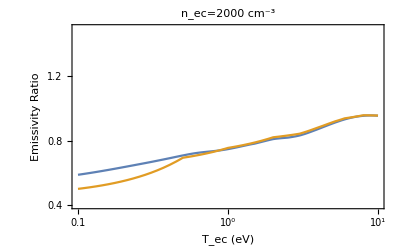
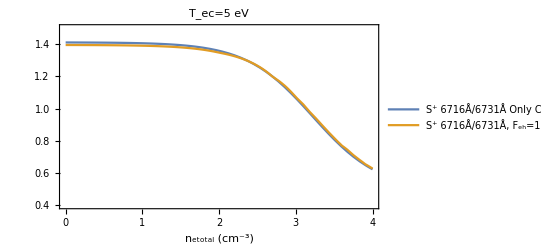
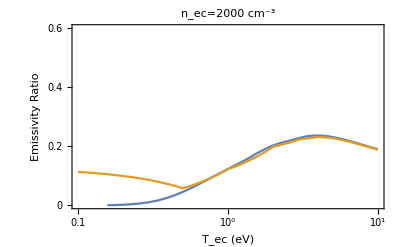
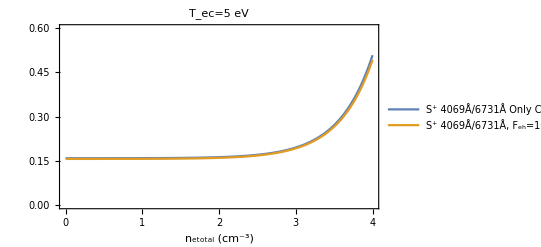
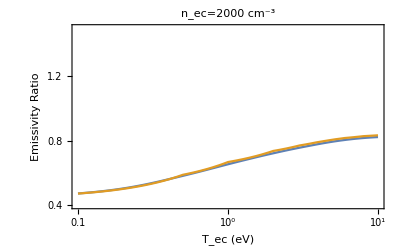
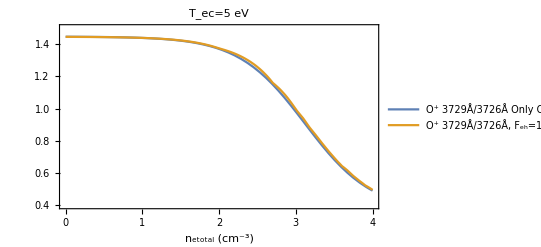
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

SetDirectory["/Users/enerney/Desktop/emissiontables_CITEP_2_"]
nec = Flatten[Import["nec_for_ratio_plots_61_elements.csv","CSV"]];
Tec = Flatten[Import["tec_for_ratio_plots_57_elements.csv","CSV"]];

nel2 = Flatten[Import["nel_for_ratio_plots_13_elements.csv","CSV"]];
Tec2 = Flatten[Import["tec_for_ratio_plots_10_elements.csv","CSV"]];

spvstecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
spvstecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];
opvstecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_tec_at_nec=2000_percc_57_elements.csv","CSV"]];

spvsnecratio = Flatten[Import["chianti10.1_APO_sp_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
spvsnecratio2 = Flatten[Import["chianti10.1_APO_sp_emissline2_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];
opvsnecratio = Flatten[Import["chianti10.1_APO_op_emiss_ratio_vs_nec_at_Tec=5eV_61_elements.csv","CSV"]];


spvstecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.1_Teh=300eV_lowres.csv","CSV"]];
spvstecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.1_Teh=300eV_lowres.csv","CSV"]];
opvstecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_tec_at_nel=2000_percc_feh=0.1_Teh=300eV_lowres.csv","CSV"]];

spvsnecratiohote = Flatten[Import["chianti10.1_APO_sp_6716to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.1_Teh=300eV_lowres.csv","CSV"]];
spvsnecratio2hote = Flatten[Import["chianti10.1_APO_sp_4069to6731_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.1_Teh=300eV_lowres.csv","CSV"]];
opvsnecratiohote = Flatten[Import["chianti10.1_APO_op_3729to3726_emiss_ratio_vs_nel_at_Tec=5eV_feh=0.1_Teh=300eV_lowres.csv","CSV"]];



spvstecratiolist =Table[{Tec[[i]],spvstecratio[[i]]},{i,1,Length[Tec],1}];
spvstecratiolist2 =Table[{Tec[[i]],spvstecratio2[[i]]},{i,1,Length[Tec],1}];
opvstecratiolist =Table[{Tec[[i]],opvstecratio[[i]]},{i,1,Length[Tec],1}];
spvsnecratiolist =Table[{nec[[i]],spvsnecratio[[i]]},{i,1,Length[nec],1}];
spvsnecratiolist2 =Table[{nec[[i]],spvsnecratio2[[i]]},{i,1,Length[nec],1}];
opvsnecratiolist =Table[{nec[[i]],opvsnecratio[[i]]},{i,1,Length[nec],1}];

spvstecratiolisthote =Table[{Tec2[[i]],spvstecratiohote[[i]]},{i,1,Length[Tec2],1}];
spvstecratiolist2hote =Table[{Tec2[[i]],spvstecratio2hote[[i]]},{i,1,Length[Tec2],1}];
opvstecratiolisthote =Table[{Tec2[[i]],opvstecratiohote[[i]]},{i,1,Length[Tec2],1}];

spvsnecratiolisthote =Table[{nel2[[i]],spvsnecratiohote[[i]]},{i,1,Length[nel2],1}];
spvsnecratiolist2hote =Table[{nel2[[i]],spvsnecratio2hote[[i]]},{i,1,Length[nel2],1}];
opvsnecratiolisthote =Table[{nel2[[i]],opvsnecratiohote[[i]]},{i,1,Length[nel2],1}];


spvstecratioint=Interpolation[spvstecratiolist];
spvstecratioint2=Interpolation[spvstecratiolist2];
opvstecratioint=Interpolation[opvstecratiolist];

spvsnecratioint=Interpolation[spvsnecratiolist];
spvsnecratioint2=Interpolation[spvsnecratiolist2];
opvsnecratioint=Interpolation[opvsnecratiolist];

spvstecratiointhote=Interpolation[spvstecratiolisthote,InterpolationOrder->1];
spvstecratioint2hote=Interpolation[spvstecratiolist2hote,InterpolationOrder->1];
opvstecratiointhote=Interpolation[opvstecratiolisthote,InterpolationOrder->1];

spvsnecratiointhote=Interpolation[spvsnecratiolisthote,InterpolationOrder->1];
spvsnecratioint2hote=Interpolation[spvsnecratiolist2hote,InterpolationOrder->1];
opvsnecratiointhote=Interpolation[opvsnecratiolisthote,InterpolationOrder->1];

p1=Plot[{spvstecratioint[x],spvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p2=Plot[{spvsnecratioint[x],spvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"S^+ 6716Å/6731Å Only Core Electrons","S^+ 6716Å/6731Å, F_eh=10%, T_eh 300 eV"}];


p3=Plot[{spvstecratioint2[x],spvstecratioint2hote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6}];
p4=Plot[{spvsnecratioint2[x],spvsnecratioint2hote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0,0.6},PlotLegends->{"S^+ 4069Å/6731Å Only Core Electrons","S^+ 4069Å/6731Å, F_eh=10%, T_eh 300 eV"}];


p5=Plot[{opvstecratioint[x],opvstecratiointhote[x]},{x,0.1,10},Frame->True,FrameLabel->{"T_ec (eV)","Emissivity Ratio"},PlotLabel->"n_ec=2000 cm^-3",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5}];
p6=Plot[{opvsnecratioint[x],opvsnecratiointhote[x]},{x,1,10000},Frame->True,FrameLabel->{"n_etotal (cm^-3)",""},PlotLabel->"T_ec=5 eV",ScalingFunctions->{"Log10","Linear"},PlotRange->{0.4,1.5},PlotLegends->{"O^+ 3729Å/3726Å Only Core Electrons","O^+ 3729Å/3726Å, F_eh=10%, T_eh 300 eV"}];

Grid[{{p1,p2},{p3,p4},{p5,p6}}]
```

```mathematica
Tec
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.}

```mathematica
nec
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,200.,300.,400.,500.,750.,1000.,1250.,1500.,1750.,2000.,2250.,2500.,2750.,3000.,3250.,3500.,3750.,4000.,4250.,4500.,4750.,5000.,5250.,5500.,5750.,6000.,6250.,6500.,6750.,7000.,7250.,7500.,7750.,8000.,8250.,8500.,8750.,9000.,9250.,9500.,9750.,10000.}

```mathematica
MinMax[spratio2list[[All,3]]]
```

{1.80118,903884.}

```mathematica
MinMax[spratio3list[[All,3]]]
```

{5.74698,2.72256×10^6}

```mathematica
Tec
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.}

```mathematica
Tec={0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7000000000000001,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.}
```

{0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.}

{0.01,{0.01,0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,25.,30.,35.,40.,45.,50.,55.,60.,80.,100.,120.,140.,160.,180.,200.,280.,360.,440.,520.,600.}}